```mathematica
g = 9.8;
l = 3;
m = 1;
k = 2;
```

```mathematica
solutions = NDSolveValue[
{
r''[t]==r[t] θ'[t]^2+g Cos[θ[t]]-k/m (r[t]-l),
r[t]*θ''[t]+ 2r'[t]*θ'[t]+g Sin[θ[t]]==0,
r[0] == 1,r'[0]==6,
θ[0] == π/3, θ'[0]==10
},
{r[t],θ[t]},
{t,0,100}
];
```

```mathematica
rV[r_,θ_]:={r Sin[θ],-r Cos[θ]};
rV[tp_]:=Apply[rV,solutions/.t->tp];
```

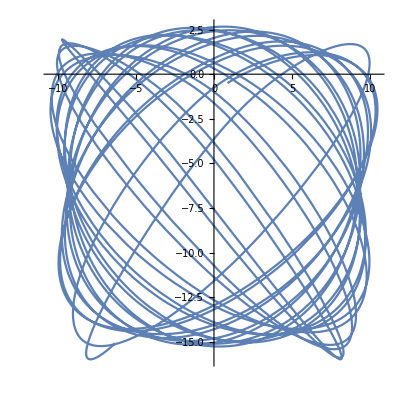

```mathematica
ParametricPlot[rV[t],{t,0,100},AspectRatio->1]
```

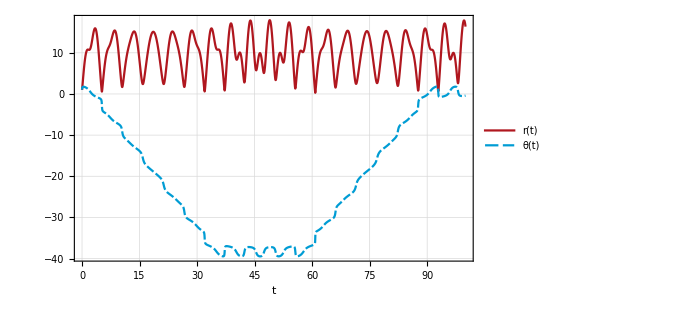

```mathematica
Plot[solutions,{t,0,100},
PlotRange->All,
PlotLegends->{"r(t)","θ(t)"},
PlotTheme->"Monochrome",
FrameLabel->{Style["t",15], Style["",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
Frame->True,
ImageSize->500,
PlotStyle->{RGBColor[0.689993, 0.089999, 0.119999],RGBColor[0, 0.61, 0.8300000000000001]}
]
```

```mathematica
solutionsPhaseSpace = NDSolve[
{
r''[t]==r[t] θ'[t]^2+g Cos[θ[t]]-k/m (r[t]-l),
r[t]*θ''[t]+ 2r'[t]*θ'[t]+g Sin[θ[t]]==0,
r[0] == 1,r'[0]==6,
θ[0] == π/3, θ'[0]==10
},
{r[t],θ[t]},
{t,0,100}
];
```

```mathematica
solutionsPhaseSpace
```

{{r[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t]}}

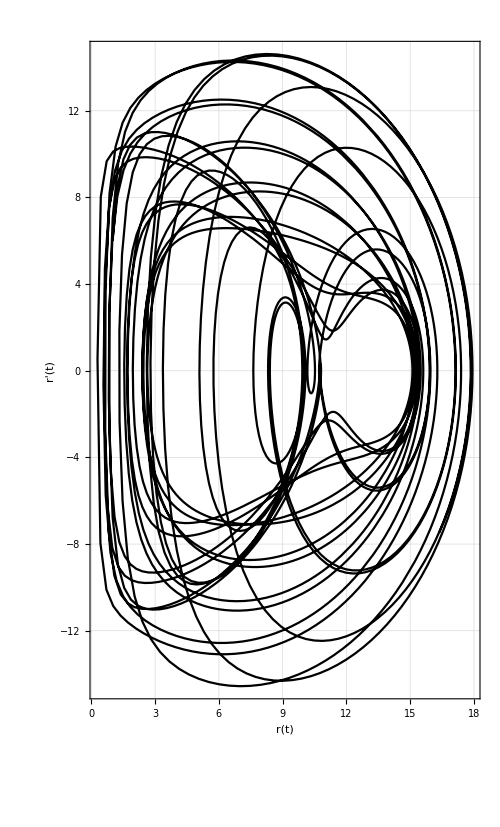

```mathematica
ParametricPlot[
{InterpolatingFunction[…][t],InterpolatingFunction[…]'[t]},{t,0,100},
PlotRange->All,
PlotTheme->"Monochrome",
FrameLabel->{Style["r(t)",15], Style["r'(t)",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
Frame->True,
ImageSize->500
]
```

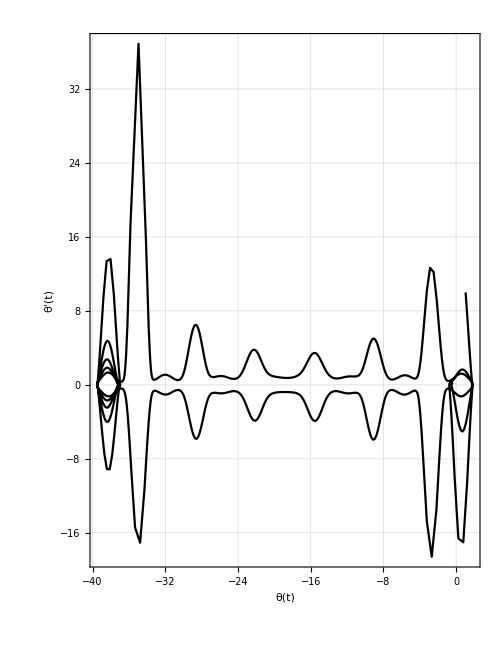

```mathematica
ParametricPlot[
{InterpolatingFunction[…][t],InterpolatingFunction[…]'[t]},{t,0,100},
PlotRange->All,
PlotTheme->"Monochrome",
FrameLabel->{Style["θ(t)",15], Style["θ'(t)",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
Frame->True,
ImageSize->500
]
```

```mathematica
DropSides[l_List]:=Take[l,{2,-2}];
AppendSides[l_List,left_,right_]:=Join[{left},l,{right}];
OddEven[l_List]:=Flatten[Partition[l,2,2,1,{}],{2}]; (* Source: https://mathematica.stackexchange.com/questions/21468/pretty-way-to-group-elements-at-odd-and-even-positions *)
Spring[{xi_,yi_},{xf_,yf_},div_,width_]:=Block[{xPoints,slope,xyPoints,d,odd,even,normalPointsOdd,normalPointsEven,zigzagPts,springCoords},
xPoints = Range[xi,xf-xi,(xf-xi)/div];
slope = (yf-yi)/(xf-xi);
xyPoints = Table[{x,slope(x-xi)+yi},{x,DropSides[xPoints]}];
{odd,even} = OddEven[xyPoints];
d = width*Normalize[{xf-xi,yf-yi}];
normalPointsOdd = Map[RotationMatrix[π/2].d+#&,odd];
normalPointsEven = Map[RotationMatrix[-π/2].d+#&,even];
zigzagPts = Riffle[normalPointsOdd,normalPointsEven];
springCoords = AppendSides[zigzagPts,{xi,yi},{xf,yf}];

Line[springCoords]
];
Diagram[r_]:=Graphics[
{
Brown,Line[{{-1,0},{1,0}}],
Black,Spring[{0,0},r,10,0.4],
Green,Disk[r,0.4]
},
PlotRange->{{-15,15},{-20,10}}
];
```

```mathematica
Manipulate[Diagram[rV[t]],{t,0,10}]
```

### Gráfica según los parámetros

```mathematica
PlotSolution[r0_,rP0_,θ0_,θP0_,tMax_]:=DynamicModule[{solutions,rVec},
solutions = NDSolveValue[
{
r''[t]==r[t] θ'[t]^2+g Cos[θ[t]]-k/m (r[t]-l),
r[t]*θ''[t]+ 2r'[t]*θ'[t]+g Sin[θ[t]]==0,
r[0] == r0,r'[0]==rP0,
θ[0] ==θ0, θ'[0]==θP0
},
{r[t],θ[t]},
{t,0,tMax}
];

rVec[r_,θ_]:={r Sin[θ],-r Cos[θ]};
rVec[tp_]:=Apply[rVec,solutions/.t->tp];

ParametricPlot[rVec[t],{t,0,tMax},PlotRange->All]
];
PlotDynamicSolution[r0_,rP0_,θ0_,θP0_,tMax_]:=DynamicModule[{solutions,rVec},
solutions = NDSolveValue[
{
r''[t]==r[t] θ'[t]^2+g Cos[θ[t]]-k/m (r[t]-l),
r[t]*θ''[t]+ 2r'[t]*θ'[t]+g Sin[θ[t]]==0,
r[0] == r0,r'[0]==rP0,
θ[0] ==θ0, θ'[0]==θP0
},
{r[t],θ[t]},
{t,0,tMax}
];

rVec[r_,θ_]:={r Sin[θ],-r Cos[θ]};
rVec[tp_]:=Apply[rVec,solutions/.t->tp];

Manipulate[
Show[
Diagram[rVec[tp]],
ParametricPlot[rVec[t],{t,0,tp}]
],
{tp,0.0001,tMax}
]
];
```

```mathematica
PlotDynamicSolution[3,0,π/3,-4,60]
```

```mathematica
PlotDynamicSolution[3,5,π/3,-6,160]
```

```mathematica
PlotDynamicSolution[1,5,π/3,-6,160]
```

```mathematica
Manipulate[
PlotSolution[r0,rP0,θ0,θP0,160],
{{r0,3},0.01,20},
{{rP0,5},0,40},
{{θ0,π/3},-π/2,π/2},
{{θP0,-3},-20,20}
]
```

#### Péndulo simple

```mathematica
sol = NDSolve[{θ''[t]+g/l Sin[θ[t]]==-θ'[t],θ[0]==1,θ'[0]==0},{θ[t]},{t,0,10}]
```

{{θ[t]→InterpolatingFunction[…][t]}}

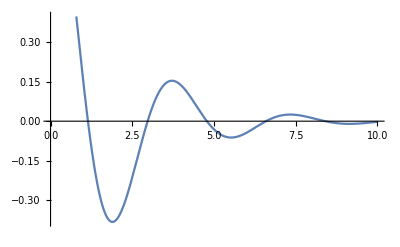

```mathematica
Plot[InterpolatingFunction[…][t],{t,0,10}]
```

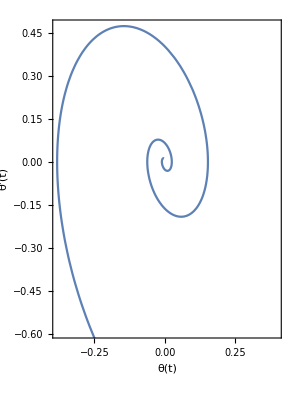

```mathematica
ParametricPlot[{InterpolatingFunction[…][t],InterpolatingFunction[…]'[t]},{t,0,10},Frame->True,FrameLabel->{"θ(t)","θ'(t)"}]
```